```mathematica
DrawAllSolutionsAndNonSolutions[g_,imagesize_:350]:=Block[{edges,nonedges,bad, good,all, goodcolored, badcolored},
edges=EdgeList[g];
bad=DeleteDuplicates[Flatten[Join[Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,edges}]]]];
nonedges=EdgeList[GraphComplement[g]];
good=DeleteDuplicates[Flatten[Join[Table[Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]],{e,nonedges}]]]];
all=Append[Join[good,bad],SetsToSymbol[Table[{k},{k,VertexCount[g]}]]];
goodcolored=Table[e->Blue,{e,good}];
badcolored=Table[e->Red,{e,bad}];
Graph[FormulaGraphReverse2[all],VertexLabels->"Name",VertexStyle->Join[goodcolored,badcolored]]
]
```

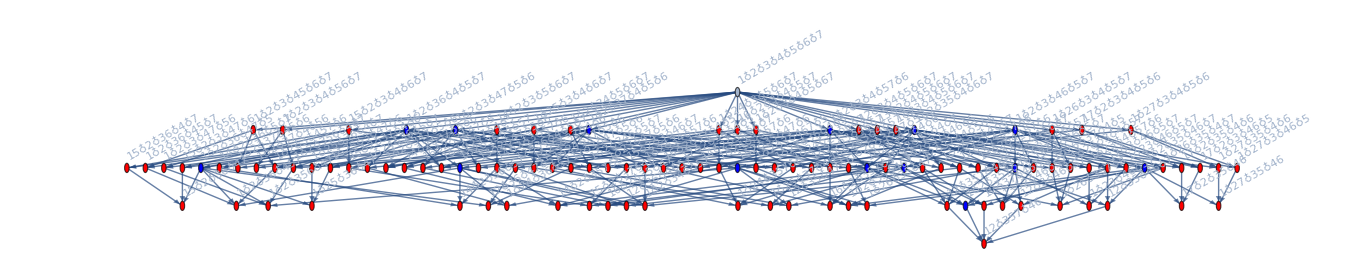

```mathematica
DrawAllSolutionsAndNonSolutions[MinimalGraph[6]]
```

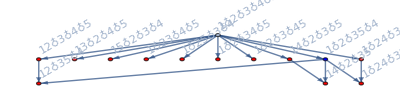

```mathematica
DrawAllSolutionsAndNonSolutions[MinimalGraph[4]]
```